```mathematica
Thomas' cyclically symmetric attractor
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
timepiecefx[t]:=Piecewise[{
{-1,500>=t>0},
{1,1200>=t>500},
{-1,1500>=t>1200},
{1,1800>=t>1500},
{-1,2400>=t>1800},
{1,2600>=t>2400},
{-1,3400>=t>2600},
{1,4200>=t>3400},
{-1,4800>=t>4200},
{1,5000>=t>4800},
{-1,5500>=t>5000},
{1,6000>=t>5500},
{-1,6700>=t>6000},
{1,7500>=t>6000}
}]

tend=7500;
eq={x'[t]==Sin[y[t]]-b*(.235+.055timepiecefx[t]) *x[t],y'[t]==Sin[z[t]]-b*(.235+.055timepiecefx[t])*y[t],z'[t]==Sin[x[t]]-b*(.235+.055timepiecefx[t])*z[t]};
init={x[0]==10,y[0]==10,z[0]==1};
pars={b-> 1};
{xs,ys,zs}=NDSolveValue[{eq/. pars,init},{x,y,z},{t,0,tend}];
ParametricPlot3D[{xs[t],ys[t],zs[t]},{t,0,tend},PlotStyle->Thickness[.001]]
```

-Graphics3D-

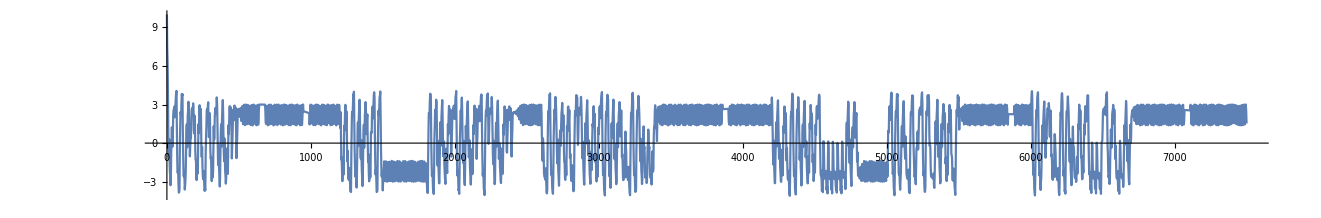

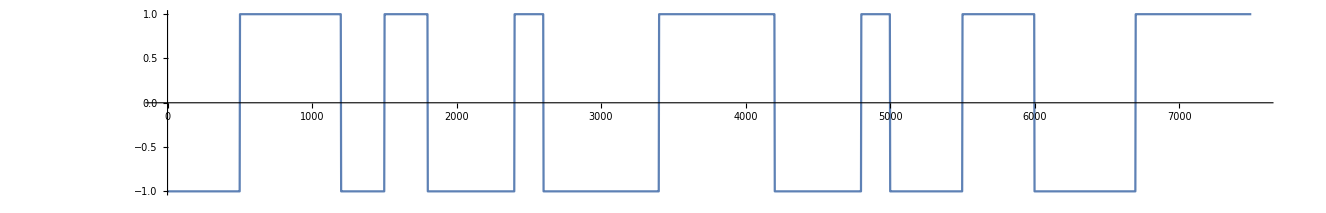

```mathematica
Plot[xs[t],{t,0,7500}]
Plot[Piecewise[{
{-1,500>=t>0},
{1,1200>=t>500},
{-1,1500>=t>1200},
{1,1800>=t>1500},
{-1,2400>=t>1800},
{1,2600>=t>2400},
{-1,3400>=t>2600},
{1,4200>=t>3400},
{-1,4800>=t>4200},
{1,5000>=t>4800},
{-1,5500>=t>5000},
{1,6000>=t>5500},
{-1,6700>=t>6000},
{1,7500>=t>6000}
}],{t,0,7500}]
```

```mathematica
Export["yourpath/thomas.csv",Table[Flatten[{t,xs[t],ys[t],zs[t]}],{t,0,tend}]]
```